# Expected R^2

```mathematica
ta0=RandomVariate[StudentTDistribution[1],10^4];
```

```mathematica
ta1=RandomVariate[NormalDistribution[],10^4];
```

```mathematica
ta2=(a ta1 + b) + ta0 /. {a->10^3,b->299};
ta3=Transpose[{ta1,ta2}];
```

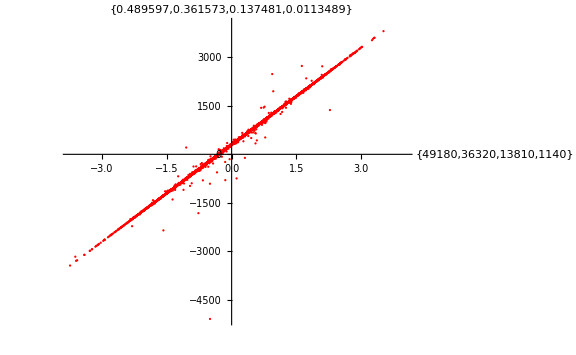

```mathematica
ListPlot[ta3, PlotStyle->Red,AxesLabel->{X,Y},
ImageSize->Large]
```

```mathematica
lm=LinearModelFit[ta3,x,x]
```

FittedModel[303.083+998.068 x]

```mathematica
res=lm["FitResiduals"];
```

```mathematica
lm["RSquared"]
```

0.775144

```mathematica
{1-Total[res^2]/Total[(ta2-Mean[ta2])^2],a^2/(a^2+Mean[res^2])}/.{a->10^3,b->299}
```

{0.775144,0.780189}